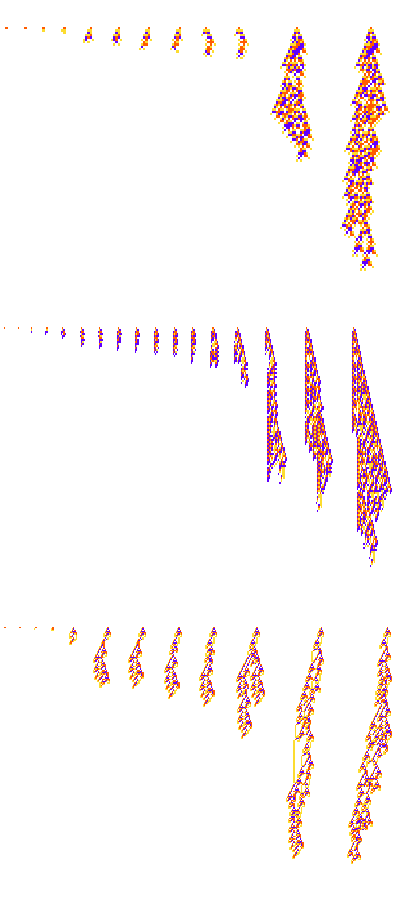

```mathematica
Column[MapThread[
Function[{evo, steps}, GraphicsRow[PlotCA[ArrayPad[#, 3]&/@CellularAutomaton[#, {{1}, 0}, steps],FrameStyle->Directive[Thin,Gray], "Trim"->{2, None}]&/@evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]], 1]], Spacings->10, ImageSize->{600, Automatic}]], {evos, {105, 120, 190}}]]
```

What about the rate of evolution? Looking just at the progressive fitness in our evolutions, we can see how the organisms “climb” different fitness hills and then plateau at some point, similar to what’s observed in biology:

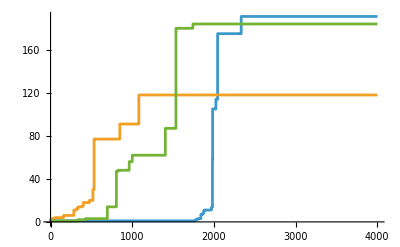

```mathematica
ListStepPlot[evos[[All, All, -1]]]
```

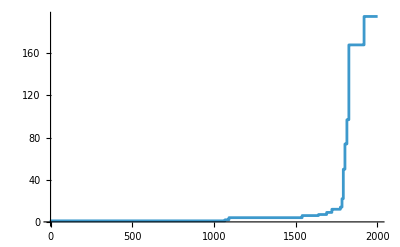

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

And from this, we can see that the main problem that adaptive evolution is solving in this case is growth inhibition. And because of that, our evolved organisms exhibit much more of a “worm-like” shape then the random group.

I want to discuss here is the nature of the observed patterns. How do these sets of rules and patterns achieve their goal of living some number of steps and then terminating?

To get at this, we can look at an adaptively evolved set of organisms:

And compare that to a random sample of our rule space:

```mathematica
GraphicsGrid[Catenate[Table[PlotCA[PerturbedCellularAutomaton[#, {{1}, 0}, {200, {-30, 30}}], "Trim"->{None, None},ImageSize->{Automatic, 100}], 5]&/@ #]&/@Partition[rob[[sortedidxs[[;;10]], 1]], 2]]
```

-Graphics-

```mathematica
GraphicsGrid[Table[PlotCA[PerturbedCellularAutomaton[#, {{1}, 0}, {200, {-100, 100}}], "Trim"->{None, None},"MaxWidth"->{80, 150},ImageSize->{Automatic, 100}], 10]&/@rob[[sortedidxs[[;;3]], 1]]]
```

-Graphics-

```mathematica
SeedRandom[4444];GraphicsGrid[Table[PlotCA[PerturbedCellularAutomaton[#, {{1}, 0}, {200, {-100, 100}}], "Trim"->{1, None},ImageSize->{Automatic, 200}], 15]&/@rob[[sortedidxs[[;;3]], 1]]]
```

-Graphics-

```mathematica
PlotCA/@(CellularAutomaton[reg[[#, 1]], {{1}, 0}, 200]&/@sireg[[45;;55]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Labeled[PlotCA[#], TestCALifeTime[#]]&/@(CellularAutomaton[reg[[#, 1]], {{1}, 0}, 200]&/@sireg[[45;;75]])
```

{-Graphics-191,-Graphics-191,-Graphics-191,-Graphics-191,-Graphics-190,-Graphics-190,-Graphics-190,-Graphics-190,-Graphics-189,-Graphics-189,-Graphics-189,-Graphics-189,-Graphics-188,-Graphics-187,-Graphics-185,-Graphics-184,-Graphics-182,-Graphics-181,-Graphics-181,-Graphics-181,-Graphics-180,-Graphics-179,-Graphics-179,-Graphics-178,-Graphics-178,-Graphics-176,-Graphics-175,-Graphics-175,-Graphics-174,-Graphics-173,-Graphics-173}

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,rob[[sortedidxs[[;;10]], 1]]];
```

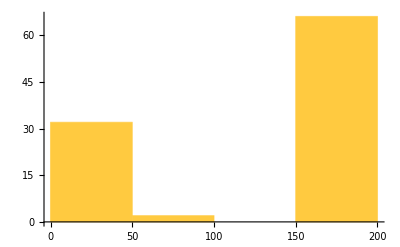

```mathematica
Histogram[( samplts/.-Infinity->0)[[1]]]
```

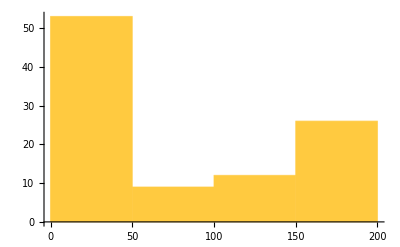
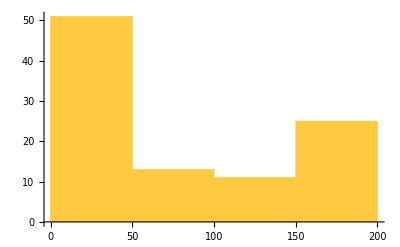
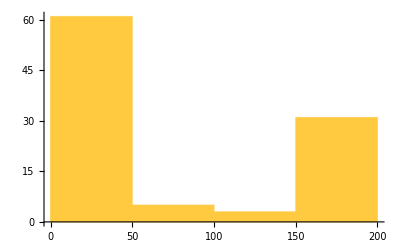
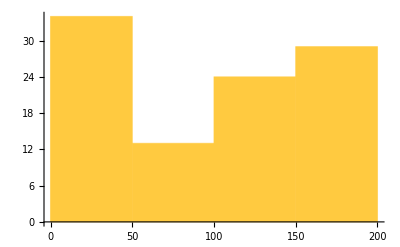
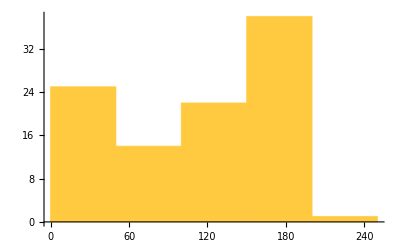
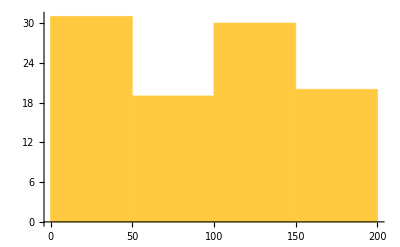
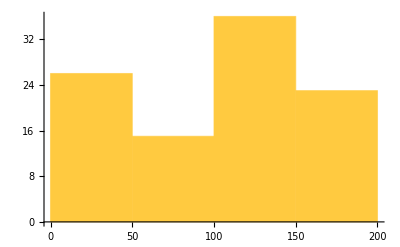
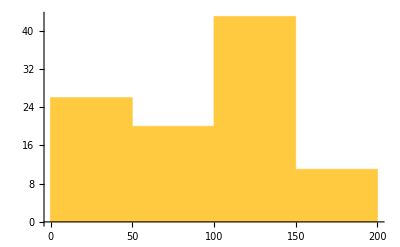
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram/@( samplts/.-Infinity->0)
```

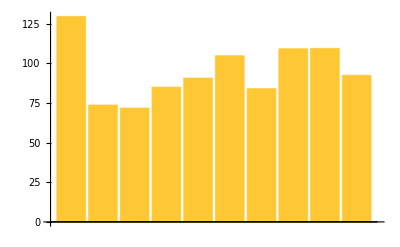

```mathematica
BarChart[N/@Mean/@(samplts/.-Infinity->0)]
```

```mathematica
GraphicsGrid[Partition[Histogram[#, {5}]&/@(samplts/.-Infinity->0), 5]]
```

-Graphics-

```mathematica
Histogram[(samplts/.-Infinity->0),{5}, ChartLayout->{"Row", 2}, FrameStyle->Directive[Thickness[.001], Lighter[Gray]]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[#,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  Table[{i, 10i}, {i, 0,20, 5}], None], Automatic}}, BarSpacing->None, ImageSize->{If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  205, 215], Automatic}]&, MapAt[Style[#, (*Lighter[Red, .3]*)Red]&, BinCounts[#, {10}]&/@(samplts[[;;6]]/.-Infinity->210), {All, -1}]], 3], Spacings->0]
```

-Graphics-

```mathematica
Histogram[(samplts[[;;6]]/.-Infinity->205),{5}, ChartLayout->{"Row", 3}, ImageSize->{650, Automatic}]
```

-Graphics-

```mathematica
Grid[Partition[MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]], PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above, Appearance->None]] ,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[4 <=#2[[1]] <= 6,  Table[{i, 5i}, {i, 0,50, 10}], None], Automatic}}, BarSpacing->None,ImageSize->{If[#2[[1]] == 1 || #2[[1]] == 4,240, 220], Automatic} , LabelingSize->100, PlotRange->150, PlotRangePadding->{Automatic, 0},
Epilog->{Dotted, Red, Line[{{means[[bmi[[#2[[1]]]]]]/5, 100}, {means[[bmi[[#2[[1]]]]]]/5, 0}}]}
]&, 
MapAt[Style[#,Red]&, BinCounts[#, {5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210), {All, -1}]], 3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[8890];
GraphicsRow[Table[{{"[◼]", "PlotCA"}}[With[{ru=l1[[bmi[[1]], 1]]},{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-20,35}},1]],"ArrowSize"->Small(*,"Trim"->{2,None}*),ImageSize->{Automatic,400}],{i,6}]]
```

-Graphics-

```mathematica
SeedRandom[1114];
ResourceFunction["InteractiveListSelector"][{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #] ,"ArrowSize"->Small]&, RandomSample[allperts[l1[[bmi[[1]], 1]], {{1}, 0}, {200, {-200, 200}}], 30]]
```

{<|{40,202}→0|>}

```mathematica
<|{123,214}->2|>
```

```mathematica
<|{40,202}->0|>
```

```mathematica
<|{41,196}->2|>
```

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #] ,"ArrowSize"->Small]&/@{<|{89,201}->1|>,<|{82,206}->2|>,<|{135,215}->1|>,<|{79,208}->0|>,<|{79,208}->0|>,<|{105,213}->2|>,<|{79,208}->0|>,<|{22,199}->0|>,<|{41,196}->2|>}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[With[{ru=First@#},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-20,70}},1]],"ArrowSize"->Small,"Trim"->{2,None},ImageSize->{Automatic,400}],{i,14}]&/@l1[[bmi[[;;4]]]]]
```

-Graphics-

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[With[{ru=First@#},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-20,40}},1]],"ArrowSize"->Small,"Trim"->{2,None},ImageSize->{Automatic,400}],{i,14}]&/l1[[bmi[[;;4]]]]]
```

-Graphics-

To get at this we can look at the distribution of lifetimes

So how did these automaton manage to deal with perturbations?

We can do some sample perturbations to the three longest patterns to get a sense of this:

```mathematica
SeedRandom[999999];
GraphicsGrid[Table[PlotCA[PerturbedCellularAutomaton[#, {{1}, 0}, {200, {-100, 100}}], "Trim"->{None, None},"MaxWidth"->{80, 180},ImageSize->{Automatic, 100}], 10]&/@rob[[sortedidxs[[;;3]], 1]]]
```

-Graphics-

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[With[{ru=First@#},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-20,40}},1]],"ArrowSize"->Small,"Trim"->{2,None},ImageSize->{Automatic,400}],{i,14}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{179079137400185473786391819702541282316,4,1},111},{{268421576596783154125046530204266236812,4,1},111},{{113554917644982243172837530688048101952,4,1},103}}]
```

So we can see that the top one (which has a visibly unique structure that we’ll discuss later) seems to be able to stay very close to it’s original length for many perturbations, but still runs over for a few of them. The other two seem to be far more sensitive to perturbations. Comparing this to automata of similar length that were evolved regularly, we get:

```mathematica
GraphicsGrid[Table[PlotCA[PerturbedCellularAutomaton[#, {{1}, 0}, {200, {-100, 100}}], "Trim"->{None, None},"MaxWidth"->{80, 180},ImageSize->{Automatic, 100}], 10]&/@reg[[sireg[[{45, 65, 75}]], 1]]]
```

-Graphics-

So we can see that the regularly evolved patterns are somewhat less robust (especially compared to the big yellow automaton) to perturbation, and quite often, overrun the cut-off length.

Another way to get at this is to look at the distribution of lifetimes under perturbation. Here are all the distributions, sorted by mean lifetime under perturbation (excluding infinities), for the robust group:

From these it’s not very clear at all what’s going on. To get a better sense, we can look at the distribution of lifetimes for our longest lived automata, and pick out the patterns that are the most robust:

And there are two key features that make this possible. First, the simplicity of the yellow section means that there are limited “failure-states” of the system, so even if we move the perturbation location, or change the color, there are only nine potential new rules that can come about:

```mathematica
GraphicsGrid[Transpose[Partition[Show[#, ImageSize->Small]&/@(RulePlot[CellularAutomaton[l1[[bmi[[1]], 1]]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten)[[{2, 3, 4, 5, 9, 13, 17, 33, 49, 1}]], 3]], Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]
```

-Graphics-

Looking at the case of a blue change, we can draw a causal graph between different rules:

```mathematica
GraphicsRow[Module[{ca = First[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {{75, 110}, {-200, 200}}, <|#|>]]},
{{left, right}, bottom} = gettrimoffsets[ca, {1, None}]; {{"[◼]", "PlotCA"}}[ca , "Graphics"->getarrow[ca, {#[[1, 1]] - 75,#[[1, 2]]}, left, bottom, "Left"]]]&/@ {{82 ,206}->2,{85 ,215}->0, {95 ,206}->1}]
```

-Graphics-

Secondly, there needs to be a mechanism for steering the system back to it’s original state, despite a small change to the pattern. In this case this is done by this rule:

And in fact, we can do a whole bunch of perturbations, even though this wasn’t in the “training set”, and still stay pretty close to the original lifetime:

```mathematica
SeedRandom[3336];
Module[{rps = Transpose[{RandomInteger[{80, 90}, 10], RandomInteger[{205, 215}, 10]}], pcas},
pcas =PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {#, {-200, 200}}, Thread[rps->"Random"]]&/@ {200, {75, 111}};
GraphicsRow[MapIndexed[PlotCA[If[#2[[1]] == 1,#, #[[1]]],   "Graphics"->If[#2[[1]] == 1, {}, (getarrow[pca[[1]], {#[[1, 1]] - 76,#[[1, 2]]}, left, bottom, "Left"]&)/@ Normal[#[[-1]]]],"ArrowSize"->Small, ImageSize-> If[#2[[1]] == 1, Automatic, 210] ]&, pcas], Alignment->{Center, Automatic}]]
```

-Graphics-

So in our evolution, we only made single bit changes to the system, but interestingly, this automaton is also able to deal with multiple perturbations, in machine learning terms, it “generalized” away from

Interestingly, if we do a perturbation in an all-white environment, this is not true:

```mathematica
init = {0, 0, 0, 0, 1, 0, 0, 0, 0};
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 0], 3, 1]
```

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{0, 0, 0}}], 6];
```

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[ArrayPlot[{#2[[2]]}, ImageSize->30,ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]], #1]&), VertexCoordinates->Catenate[Table[{j, i}, {i,Length[tab], 1, -1}, {j,1, Length[tab[[1]]]}]]]
```

-Graphics-

we can see how the yellow rules are like “insulation”, preventing any potentially harmful patterns from propagating outside of the area, and the only pattern that can escape is the relatively harmless red streak.

```mathematica
lts2 = With[{aps = allperts[reg[[43, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts2]
```

```mathematica
lts2 = ;
```

```mathematica
byidx = Partition[lts2/.-Infinity->280, 3];
```

```mathematica
blt = Max/@byidx;
```

```mathematica
GraphicsRow[Reverse@{
Module[{ca =ArrayPad[#, 1]&/@ CellularAutomaton[reg[[43, 1]], {{1}, 0},120], lt},
lt = TestCALifeTime[ca];
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, Abs[(# - lt)] / lt]]&)]],
PlotCA[PerturbedCellularAutomaton[reg[[43, 1]], {{1}, 0}, {120, {-200, 200}}, {}], MeshStyle->Opacity[.1]]}]
```

-Graphics-

```mathematica
lts3 = With[{aps = allperts[reg[[181, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
lts3 = ;
```

```mathematica
byidx = Partition[lts3/.-Infinity->400, 3];
```

```mathematica
blt = Max/@byidx;
```

```mathematica
GraphicsRow[Reverse@{
Module[{ca =ArrayPad[#, 1]&/@ CellularAutomaton[reg[[181, 1]], {{1}, 0},200], lt},
lt = TestCALifeTime[ca];
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, Abs[(# - lt)] / lt]]&)]],
PlotCA[PerturbedCellularAutomaton[reg[[181, 1]], {{1}, 0}, {200, {-200, 200}}, {}], MeshStyle->Opacity[.1]]}]
```

-Graphics-

```mathematica
lts4 = With[{aps = allperts[reg[[41, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
Iconize[lts4]
```

```mathematica
byidx = Partition[lts4/.-Infinity->295, 3];
```

```mathematica
blt = Max/@byidx;
```

```mathematica
GraphicsRow[Reverse@{
Module[{ca =ArrayPad[#, 1]&/@ CellularAutomaton[reg[[41, 1]], {{1}, 0},110], lt},
lt = TestCALifeTime[ca];
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, Abs[(# - lt)] / lt]]&)]],
PlotCA[PerturbedCellularAutomaton[reg[[41, 1]], {{1}, 0}, {110, {-200, 200}}, {}], MeshStyle->Opacity[.1]]}]
```

-Graphics-

```mathematica
lts2 = With[{aps = allperts[reg[[43, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
lts2 = ;
```

```mathematica
lts3 = With[{aps = allperts[reg[[181, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
lts3 = ;
```

```mathematica
lts4 = With[{aps = allperts[reg[[41, 1]], {{1}, 0}, {400, {-200, 200}}]}, ParallelMap[TestCALifeTime[PerturbedCellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {400, {-200, 200}}, #]]&, aps]];
```

```mathematica
lts4 = ;
```

```mathematica
GraphicsRow[MapThread[Function[{rule, lts}, 
Module[{(*cal,ca, lt, byidx, blt*)},
cal =ArrayPad[#, 1]&/@ CellularAutomaton[rule, {{1}, 0}, 400];
lt = TestCALifeTime[cal];
ca = CellularAutomaton[rule, {{1}, 0}, lt + 5];
byidx = Partition[lts/.-Infinity->400 - lt, 3];
blt = Max/@byidx;
GraphicsRow[{
PlotCA[ca],
ArrayPlot[
ReplacePart[Array[-1&, Dimensions[ca]], Thread[Catenate[bodyidxs[ca]]->blt]] ,ColorFunctionScaling->False,ColorFunction->(If[#==-1,White, Blend[{LightYellow, Yellow,  Orange, Red}, Abs[(# - lt)] / lt]]&)]
}]
]],{{ reg[[43, 1]],reg[[181, 1]], reg[[41, 1]]}, {lts2, lts3, lts4}}]]
```

Looking at some of these rules starting from random initial conditions, we can see that they are using a similarly purposeful mechanism:

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[PerturbedCellularAutomaton[#[[1]], {{1}, 0}, {200,{-200, 200}}]], 5]&/@[[{1, 2,8}]]]
```

-Graphics-

```mathematica
TestCALifeTime[CellularAutomaton[#, {{1}, 0}, 200]]&
```